HITS Linear Algebra Formulation

## The Example Graph

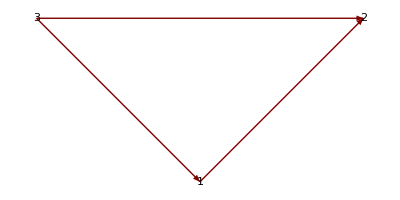

```mathematica
g = {1 -> 2, 3->2 , 3->1};
LayeredGraphPlot[g, Left, VertexLabeling->True]
```

## The Adjacency/Link Matrix

```mathematica
A = AdjacencyMatrix[g];
MatrixForm[A];
MatrixForm[Transpose[A]];
```

(0 | 1 | 0
0 | 0 | 0
1 | 1 | 0)

A

(0 | 0 | 1
1 | 0 | 1
0 | 0 | 0)

A^T

## Initialization

```mathematica
n = VertexCount[g];
a = ConstantArray[1/Sqrt[n],n];
h = ConstantArray[1/Sqrt[n],n];
MatrixForm[a];
MatrixForm[h];
```

(1/(√3)
1/(√3)
1/(√3))

a

(1/(√3)
1/(√3)
1/(√3))

h

## Iterative Recurrence Formula

h = λA.a

a = μA^T.h

λ = 1/(∑_i h_i)

μ = 1/(∑_i a_i)

```mathematica
iterations = 100;
For[i=0,i<iterations,i++,
lambda = 1/Total[h];
mu = 1/Total[a];
h1 = h;
h = lambda*N[A.a];
a = mu*N[Transpose[A].h1];
];
```

## The Resulting Authority and Hub scores

```mathematica
MatrixForm[a];
MatrixForm[h];
```

(0.618034
1.
0.)

a

(0.618034
0.
1.)

h

## Comparison With Mathematica’s Built-in Function

```mathematica
{a1,h1} = HITSCentrality[g];
MatrixForm[a1];
MatrixForm[h1];
```

(0.381966
0.618034
0.)

a

(0.618034
0.
1.)

h

## Comparison with Principal EigenVectors

a should be the principal eigenvector of A^T A and h should be the principal eigenvector of AA^T

```mathematica
{AV1, AEV1} = Eigensystem[Transpose[A].A,1];
{HV1, HEV1} = Eigensystem[A.Transpose[A],1];
MatrixForm[AEV1];
MatrixForm[HEV1];
```

(1/2 (-1+√5) | 1 | 0)

Principal Eigenvector of A^T A

(1/2 (-1+√5) | 0 | 1)

Principal Eigenvector of AA^T

Kim Hammar

kimham@kth.se

5/10 - 2017